# Clustering of Standard Candles

L. Amendola & M. Quartin 2019

This notebook evaluates the relative errors for H using the Clustering of Standards method. It requires the external file CAMB0.txt (also in this repository). Running the entire notebook requires around three minutes. Please refer to arXiv:1911:xxxxx for the details. If you use this notebook please cite that paper.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/amendola/Dropbox/active-project-Pdd.Pdv.Pvv.paper/math

## Building the Fisher matrix

```mathematica
(* build the Fisher matrix *)
(* all spectra in units of noise and include bias *)


Clear[hfid];


(* factors A and B *)
facb=dd*(1+beta*mu^2*eta^2/(mu^2*(eta^2-1)+1));faca=dv*hfid*beta*mu*eta^2/(mu^2*(eta^2-1)+1)/k/(1+z);


(* parameters; we actually use the log of these in the matrix*)
ppar={p[eta],beta,eta,sigd,sigv};
npar=Length[ppar]

(* shot noise terms *)
nd=1+1/facb^2/p[eta];
nv=1+sv2/faca^2/p[eta]; 

(* covariance matrix *) 
c=Simplify[p[eta]*{{0,facb^2*nd,0,faca*facb},{facb^2*nd,0,faca*facb,0},{0,faca*facb,0,faca^2*nv},{faca*facb,0,faca^2*nv,0}}];

invc=Simplify[Inverse[c]];

n=Length[c];

(* smoothing factors *)
dd=(1+(1/2)*(k*mu*sigd*eta)^2)^(-1/2);
dv=Sin[k*sigv*Sqrt[mu^2*(eta^2-1)+1]]/(k*sigv*Sqrt[mu^2*(eta^2-1)+1]);
```

5

```mathematica
(* Numerical  mu-averaged Fisher matrix *)

rep={p[1]->p,p'[1]->pder*k*mu^2};


dcp=Table[Simplify[D[c[[i,j]],ppar[[a]]]/.eta->1],{i,n},{j,n},{a,npar}];
gamma=Simplify[Table[invc[[i,m]]*invc[[j,l]],{i,n},{j,n},{l,n},{m,n}]/.eta->1];
fmu[p_,beta_,eta_,k_,z_,sv2_,sigd_,sigv_,pder_]=Table[Sum[ppar[[a]]*ppar[[b]]*dcp[[i,j,a]]*dcp[[l,m,b]]*gamma[[i,j,l,m]]/.eta->1,{i,n},{j,n},{l,n},{m,n}],{a,npar},{b,npar}]/.rep;


 fisher[p_,beta_,eta_,k_,z_,sv2_,sigd_,sigv_,pder_]:=(1/2)*Table[NIntegrate[fmu[p,beta,eta,k,z,sv2,sigd,sigv,pder][[a,b]],{mu,0,1}],{a,npar},{b,npar}];
```

## Fiducials and survey specifics

```mathematica
(* Read power spectrum from CAMB; the non-linear correction depends on z but  the difference is negligible *)

PSzero=Import[NotebookDirectory[]<>"CAMB0.txt","Table"];

PSfunc=Interpolation[PSzero];
kminfile=PSzero[[1,1]];
kmaxfile=PSzero[[Length[PSzero],1]];
```

```mathematica
(* fiducial cosmology and survey specifics *)

Clear[om];
omegam=0.3;
grgam=0.545; (* growth index *)
(* Hubble function fiducial *)
eh2[z_]=omegam*(1+z)^3+1-omegam;
(* Omega_matter *)
om[z_]=omegam*(1+z)^3/eh2[z];
(* growth rate *)
fgrow[z_,grgam_]=om[z]^grgam;
(* growth factor *)
gr[z_,gam_]:=Exp[-NIntegrate[fgrow[zx,gam]/(1+zx),{zx,0,z},WorkingPrecision->10,MaxRecursion->12]];

(* evolved spectrum at z *)
pskz[k_,z_]:=PSfunc[k]*gr[z,grgam]^2;
pskzder[k_,z_]:=D[PSfunc[kx],kx]*gr[z,grgam]^2/.kx->k;



(* SNe survey data *)

case=2; (* SQ *)
ndens={0.011,0.032,0.054,0.051,0.037,0.012,0.0019,0.00023}*10^(-3);

case=1; (* OPT *)
ndens={0.064,0.07,0.076,0.081,0.087,0.093,0.099,0.10}*10^(-3); 


vol={0.0459,0.296,0.727,1.27,1.88,2.51,3.13,3.72}*10^9;
zbins={0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75};
kmin={0.0175,0.0094,0.007,0.0058,0.0051,0.0046,0.0043,0.0041};
kmax={0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1};

(* k-cell gamma factor *)
gam2[k_,V_]=2*Pi/k^2/V^(2/3);


(* hx[z_]=Sqrt[eh2[z]]; *)
etax[z_]:=1; (* fiducial for HD/H_r D_r; already inserted *)
hfidx[z_]=Sqrt[eh2[z]]/3000; 


(* fiducial luminosity distance *)
dlum[z_]:=NIntegrate[1/Sqrt[eh2[zint]],{zint,0,z}];
dlump[z_]:=1/Sqrt[eh2[z]];

(* velocity shot noise *)
sigint=0.13;
svx[zx_]:=(Log[10]/5*dlum[zx]/dlump[zx]*sigint)^2+(300/300000)^2; (* should we use the same sigv here ? *)


(* assume bias1=1 *)
bias[z_]=1;
(* fiducial beta=f/bias *)
b1fid[z_]=fgrow[z,grgam]/bias[z];  

(* fiducial smoothing velocity in Mpc; values from Howlett 2017 *)
sigdx=4.24; 
sigvx=13.0;
```

## Error on H: results

```mathematica
totalerrh=Table[0,{i,Length[vol]}];
nopprime=1;
(* number of params that depend also on k , and those that don't *)
nk=2;
nz=3;



Do[{Clear[kbins];
i=0;kbins={kmax[[zshell]]};k=1;
While[k>kmin[[zshell]],{i++,k=kmax[[zshell]]-i*2*Pi/(vol[[zshell]])^(1/3),If[k>0,kbins=Append[kbins,k],0]}]; Clear[k];Print["z= ",zbins[[zshell]]];
nb=Length[kbins]-1;
hfid=hfidx[zshell];
fullmatk=Table[0,{im,nb*nk+nz},{jm,nb*nk+nz}];

Do[{matk=1/gam2[kbins[[i]],vol[[zshell]]]*fisher[bias[zshell]^2*ndens[[zshell]]*pskz[kbins[[i]],zbins[[zshell]]],b1fid[zbins[[zshell]]],etax[zbins[[zshell]]],kbins[[i]],zbins[[zshell]],svx[zbins[[zshell]]],sigdx,sigvx,bias[zshell]^2*ndens[[zshell]]*pskzder[kbins[[i]],zbins[[zshell]]]];

fullmatk=fullmatk+Table[If[((im≥nk*(i-1)+1 && im≤nk*(i-1)+nk) &&  (jm≥nk*(i-1)+1 && jm≤nk*(i-1)+nk))  
,matk[[im-nk*(i-1),jm-nk*(i-1)]],0],{im,nb*nk+nz},{jm,nb*nk+nz}]+
Table[If[
((im≥nk*(i-1)+1 && im≤nk*(i-1)+nk) &&  (jm≥nk*nb+1 && jm<=nk*nb+nz )) 
,matk[[im-nk*(i-1),jm-nk*(nb-1)]],0],{im,nb*nk+nz},{jm,nb*nk+nz}]+
Table[If[
((jm≥nk*(i-1)+1 && jm≤nk*(i-1)+nk) &&  (im≥nk*nb+1 && im<=nk*nb+nz )) 
,matk[[im-nk*(nb-1),jm-nk*(i-1)]],0],{im,nb*nk+nz},{jm,nb*nk+nz}]+
Table[If[
((im≥nk*nb+1 && im<=nk*nb+nz ) &&  (jm≥nk*nb+1 && jm<=nk*nb+nz )) 
,matk[[im-nk*(nb-1),jm-nk*(nb-1)]],0],{im,nb*nk+nz},{jm,nb*nk+nz}];

},{i,nb}];
sumfm=Inverse[fullmatk];
totalerrh[[zshell]]=Sqrt[sumfm[[-3,-3]]]},{zshell,Length[zbins]}];


"h relative errors"
Table[{zbins[[zshell]],totalerrh[[zhell]]},{zshell,Length[zbins]}]//TableForm
```

z= 0.05

z= 0.15

## Plots of relative errors

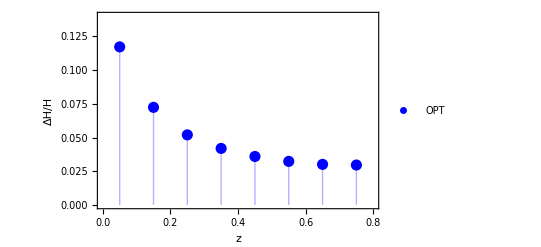

```mathematica
label=If[case==1,"OPT","SQ"];

ListPlot[{Table[{zbins[[zshell]],totalerrh[[zshell]]},{zshell, Length[zbins]}]},Frame->True,PlotStyle->{{Blue,PointSize[0.02]},{Green,PointSize[0.02]},{Red,PointSize[0.02]},{Purple,PointSize[0.02]}},PlotRange->{{0,0.8},{0,0.14}},FrameLabel->{"z","ΔΗ/H"},Filling->Axis,BaseStyle->{16,FontFamily->"Times"},PlotLegends->Placed[{label},{Right,Center}]]
```